Generating data for m0 = 0

Generating data for m0 = 1

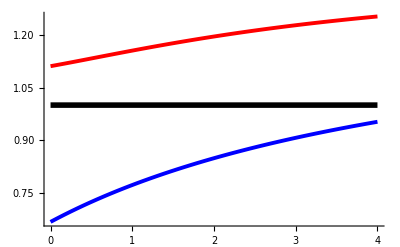

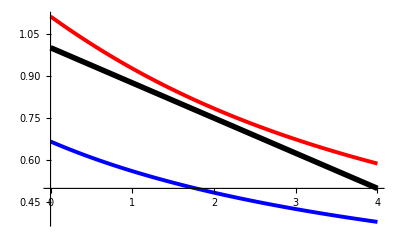

```mathematica
(* Recursive construction of expansion coefficients *)
σ1=+1; σ2=1; σ3=-1;
(* Lattice kinematics *)
LS=2;
mD[p_]:=4 Sin[1/2(2π p)/LS]^2;
(*MeanLink[λ_]:=If[λ<4,1-λ/8,2/λ];*)
MeanLink[λ_]:=1-λ/8;
m2[λ_]:=σ2/σ3(2 (1-MeanLink[λ])-σ1 λ);
G0[λ_,p_]:=1/(m2[λ]+mD[p]);
DeltaP[p_]:=If[Mod[p,LS]==0,1,0];
(* n is the number of momenta in the correlator *)
(* m is the order in the formal λ - expansion *)
(* P is the 2 n - sized list of momenta *)
G[λ_,P_,m_]:=Module[{n,Res,A,p1t,p2t,q1t,pAt,qAt,m1,m2,P1,P2,i},
n=Length[P]/2;
If[m==0,
(* We're at the bottom of the recursion - just the free propagator *)
Res=Product[1/LS DeltaP[ P[[2 i - 1]]+P[[2 i]] ] G0[λ,P[[2i-1]]] ,{i,1,n}];
,
(* Else - go to lower levels by using the SD equations *)
(* First term in the SD equation *)
Res=If[n>1,1/LS DeltaP[P[[1]]+P[[2]]] G[λ,Drop[P,2],m], 0];
(* Second term in the SD equation - switch momenta *)
For[A=2,A≤n,A++,
P1=Take[P,2(A-1)]; 
P2=Drop[P,2(A-1)];
For[p1t=0,p1t<LS,p1t++,
pAt=P[[1]]+P[[2A-1]]-p1t;
P1[[1]]=p1t; P2[[1]]=pAt;
For[m1=0,m1<m,m1++,
m2=m-m1-1;
Res+=σ2/σ3 1/LS G[λ,P1,m1] G[λ,P2,m2] ;
];
];
];
(* Third term in SD equations - join sequences with vertex *)
For[A=2,A≤n,A++,
P1=Take[P,2A]; 
P2=Drop[P,2(A-1)];
For[p1t=0,p1t<LS,p1t++,
For[pAt=0,pAt<LS,pAt++,
qAt=P[[1]]-p1t-pAt;
P1[[1]]=p1t;P1[[2A]]=qAt;P2[[1]]=pAt;
For[m1=0,m1<m,m1++,
m2=m-m1-1;
Res+=-σ2/σ3 mD[qAt] G[λ,P1,m1] G[λ,P2,m2] ;
];
];
];
];
(* Fourth term in SD equations - create vertex *)
For[p1t=0,p1t<LS,p1t++,
For[p2t=0,p2t<LS,p2t++,
q1t=P[[1]]-p1t -p2t;
P1=P;
P1[[1]]=p2t;
PrependTo[P1,q1t];
PrependTo[P1,p1t];
Res +=-(σ1 σ2)/σ3 mD[q1t] G[λ,P1,m-1];
];
];
(* Final operation *)
Res *= G0[λ,P[[1]]] ;
];
Res
];
mmax=1; λmin=0.0; λmax=4.0;
USum=Table[0,{m0,0,mmax}]; LSum=Table[0,{m0,0,mmax}];
mUSum=0; mLSum = 0;
GrU={Plot[1,{λ,λmin,λmax},PlotStyle->{Thickness[0.01],Black},PlotRange->All]};
GrL={Plot[If[λ<4,1-λ/8,2/λ],{λ,λmin,λmax},PlotStyle->{Thickness[0.01],Black},PlotRange->All]};
For[m0=0,m0≤mmax,m0++,
Print["Generating data for m0 = ",m0];
r=m0/mmax;
G00=FullSimplify[λ^(m0+1) G[λ,{0,0},m0]];
G11=FullSimplify[λ^(m0+1) G[λ,{1,1},m0]];
mUSum += (G00 + G11);
mLSum += (G00 - G11);
USum[[m0+1]]=mUSum;
LSum[[m0+1]]=mLSum;
AppendTo[GrU,Plot[mUSum,{λ,λmin,λmax},PlotStyle->{Thickness[0.007],RGBColor[r,0,1-r]},PlotRange->All]];AppendTo[GrL,Plot[mLSum,{λ,λmin,λmax},PlotStyle->{Thickness[0.007],RGBColor[r,0,1-r]},PlotRange->All]];
];
Print[Show[GrU,PlotRange->All]];
Print[Show[GrL,PlotRange->All]];
```

```mathematica
N[m2[λ]/.{λ->2.0}]
N[USum[[1]]/.{λ->2.0}]
N[LSum[[1]]/.{λ->2.0}]
```

1.5

0.848485

0.484848

```mathematica
ExtrapolationPlot[App_,λ0_,ExRes_]:=Module[{TD,i,Gr1,Gr2},
TD=Table[{1/i,App[[i]]/.{λ->λ0}},{i,1,Length[App]}];
Gr1=ListPlot[TD,PlotJoined->True,PlotStyle->{Thickness[0.01],Red},PlotRange->{{-0.05,1.0},{0.0,1.1}},DisplayFunction->Identity];
Gr2=ListPlot[TD,PlotJoined->False,PlotStyle->{PointSize[0.02],Blue},DisplayFunction->Identity];
Gr3=Graphics[{PointSize[0.03],Green,Point[{0.0,ExRes}],Gray,Line[{{0.0,ExRes},TD[[Length[TD]]]} ]}];
Show[Gr1,Gr2,Gr3,DisplayFunction->$DisplayFunction]
];
λ0=2.0;
ExtrapolationPlot[USum,λ0,1.0];
ExtrapolationPlot[LSum,λ0,1.0-λ0/8];
```